```mathematica
ϵ[N_,ξ_,y_,e_]:= e√1/(2(1-ξ) √(2(1-ξ))√(y^2-1))
```

```mathematica
y[N_,ξ_]:= 1 + (N*ξ)/(2(1-ξ))
```

```mathematica
ϵ[N_,ξ_,e_]:=ϵ[N,ξ,y[N,ξ],e]
```

```mathematica
Manipulate[Plot[ϵ[N,(2*M)/((N-1)*(N-2)),b,K],{M,10,1000}],{N,1,200,1},{b,0.2},{K,2}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

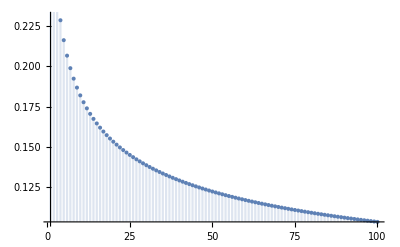

```mathematica
DiscretePlot[√3/2*1*√1/(100*(1-(2*M)/((100-1)*(100-2)))*√(100*(2*M)/((100-1)*(100-2)))), {M,1,100}]
```

```mathematica
Table[√3/2*0.99*√1/(100*(1-(2*M)/((100-1)*(100-2)))*√(100*(2*M)/((100-1)*(100-2)))), {M,1,50}]
```

{0.320025,0.269135,0.243216,0.226362,0.214102,0.204583,0.196869,0.190425,0.184919,0.18013,0.175907,0.17214,0.168747,0.165666,0.16285,0.16026,0.157866,0.155642,0.153569,0.151628,0.149805,0.148088,0.146467,0.144932,0.143475,0.14209,0.14077,0.13951,0.138306,0.137153,0.136047,0.134986,0.133965,0.132983,0.132037,0.131123,0.130242,0.12939,0.128566,0.127768,0.126995,0.126245,0.125518,0.124811,0.124125,0.123458,0.122808,0.122176,0.121561,0.120961}

```mathematica
ϵ[ξ_,e0_,x0_]:= e0√((1-x0)*√x0)/((1-ξ)*√ξ)
```

```mathematica
Manipulate[Plot[ϵ[(2*M)/((N-1)*(N-2)),e0,(2*Nc0)/((N-1)*(N-2))],{M,2,30}],{N,50,200,1},{e0,0.2},{Nc0,2}]
```